```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis5`"]];
<<GDCAnalysis3`
<<GDCComparisons`
<<GDCAnalysis5`
```

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis5.m

```mathematica
(*accEVBK=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/EVBK/gdc_VER_EVBK_points.txt"];*)accEVBK=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/E_DEDAB/POINTS/gdc_VER_EVBK_points.txt"];
accCH=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/CH/gdc_VER_CH_points.txt"];
confVAL002=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/CONF_VALUE_2/CONF_VAL_THRE_0_02.txt"];
names=Keys[accEVBK]
confs={"DOJ","Z","F"};
timesteps=Range[17];
col2=Map[Blend[{Blue, Yellow},#]&,Range[Length[timesteps]]/Length[timesteps]];
homeAdd="/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/";
spezAdd="CONF_VALUE_2/VAL_0_2/";
plotType="VAL";
revType="ALL";
(* col1=Map[ColorData["BlueGreenYellow"][#]&,Range[Length[timesteps]]/Length[timesteps]]
col3=Map[Hue[#]&,Range[Length[timesteps]]/Length[timesteps]]
col4=Map[Hue[1,#]&,Range[Length[timesteps]]/Length[timesteps]]
col5=Map[ColorData["TemperatureMap"][#]&,Range[Length[timesteps]]/Length[timesteps]]*)
```

{DLB,MUR,LYE,PHI,SED,AUS}

```mathematica
(* Dec>0.01 *)
dataDOJ=sumUpFunc[accEVBK, accCH,confVAL002,"DOJ",names,revType];
dataZ=sumUpFunc[accEVBK, accCH,confVAL002,"Z",names,revType];
dataF=sumUpFunc[accEVBK, accCH,confVAL002,"F",names,revType];
```

```mathematica
shrinkFac1=0.025;
shrinkFac2=0.15;
plotsDOJ=Map[singlePlot[#, dataDOJ,col2,shrinkFac1,shrinkFac2,plotType]&,names];
plotsZ=Map[singlePlot[#, dataZ,col2,shrinkFac1,shrinkFac2, plotType]&,names];
plotsF=Map[singlePlot[#, dataF,col2,shrinkFac1,shrinkFac2, plotType]&,names];
gridDOJ=Grid[{plotsDOJ[[1;;2]],plotsDOJ[[3;;4]],plotsDOJ[[5;;6]]}];
gridZ=Grid[{plotsZ[[1;;2]],plotsZ[[3;;4]],plotsZ[[5;;6]]}];
gridF=Grid[{plotsF[[1;;2]],plotsF[[3;;4]],plotsF[[5;;6]]}];
```

size {0.15,0.15,0.15,0.15,0.0607617,0.0658176,0.0658176,0.15}

size {0.0806853,0.0806853,0.0806853,0.05597,0.05597,0.05597,0.15,0.15,0.15}

size {0.0548334,0.0548334,0.15,0.15}

size {0.0649701,0.0558807,0.0548334,0.0695281,0.0705487,0.15}

size {0.15}

size {0.079916,0.109764,0.109764,0.15}

size {0.15,0.15,0.15,0.15,0.0599007,0.0651174,0.0651148,0.15}

size {0.0805913,0.0805949,0.0805949,0.0558272,0.0559132,0.0559139,0.15,0.15,0.15}

size {0.054774,0.0547747,0.15,0.15}

size {0.0647951,0.0557374,0.0546839,0.0694961,0.0705182,0.15}

size {0.15}

size {0.0798032,0.109735,0.109735,0.15}

size {0.15,0.15,0.15,0.15,0.139273,0.139743,0.147708,0.147592,0.146768,0.147135,0.147063,0.147472,0.148307,0.143979,0.148619,0.148614,0.15}

size {0.143738,0.144106,0.144106,0.14153,0.149812,0.14982,0.14982,0.149715,0.148062,0.147034,0.149887,0.149888,0.15,0.15,0.15}

size {0.0793762,0.0895454,0.0895454,0.0944864,0.147635,0.147725,0.148087,0.148237,0.148759,0.148736,0.149881,0.149883,0.15,0.15}

size {0.131573,0.132427,0.147066,0.146918,0.149651,0.149714,0.149702,0.1498,0.1498,0.149803,0.149936,0.149939,0.15}

size {0.147534,0.147629,0.147629,0.148352,0.148352,0.149095,0.149095,0.149106,0.149237,0.149243,0.15}

size {0.149775,0.149117,0.149942,0.149941,0.15}

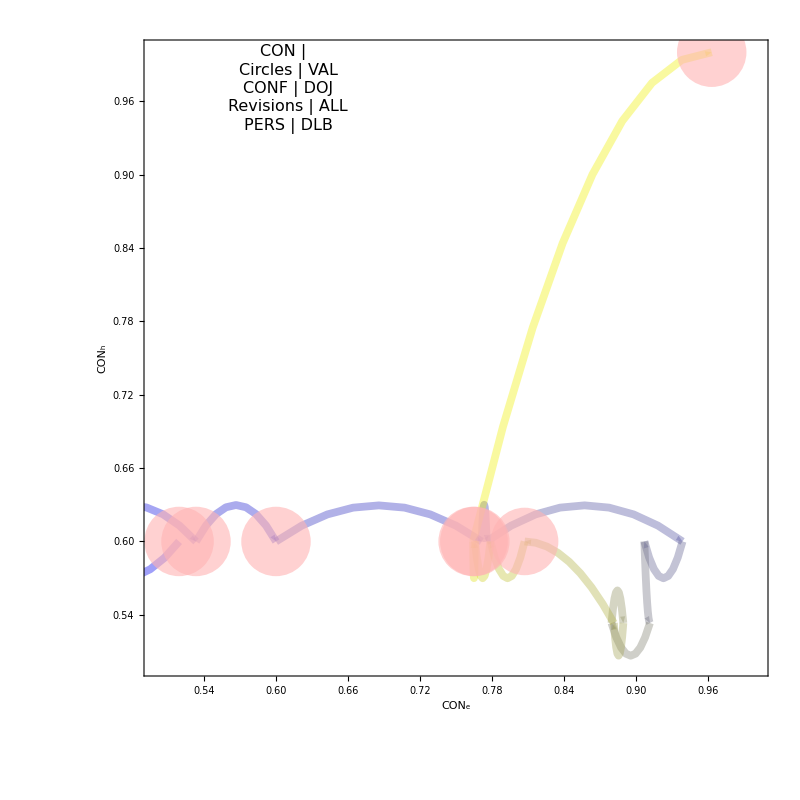

```mathematica
plotsDOJ[[1]]
```

```mathematica
SetDirectory[homeAdd<>spezAdd<>revType]
Export[ToString[plotType]<>"_DOJ.jpeg",gridDOJ]
Export[ToString[plotType]<>"_Z.jpeg",gridZ]
Export[ToString[plotType]<>"_F.jpeg",gridF]
```

/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/CONF_VALUE_2/VAL_0_2/ALL

VAL_DOJ.jpeg

VAL_Z.jpeg

VAL_F.jpeg